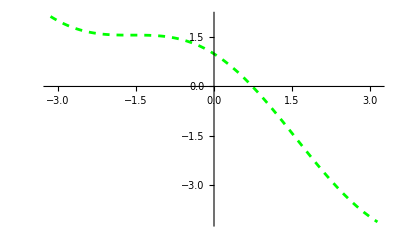

```mathematica
g[x_] := Cos[x] ;
f[x_] :=Cos[x] -x ; (* f(x) = g(x) - x *);
Plot[f[x], {x, -Pi, Pi },  PlotStyle->{Dashed, Green}]
x0 := 0.2;
xPrev := x0;
pointsf := List[{x0, f[x0]}];
pointsg := List[{x0, g[x0]}];
error := Power[10, 12];
```

```mathematica
While[ error >Power[10, -10],
(* fixed point iteration *)
xCurrent := g[xPrev];
error = Abs[f[xCurrent] ];
pointsf = Append[pointsf, {xCurrent , f[xCurrent]}];
pointsg= Append[pointsg, {xCurrent , g[xCurrent]}];
xPrev = xCurrent;
]
```

```mathematica
(*plot results*)
```

root is: 0.739085

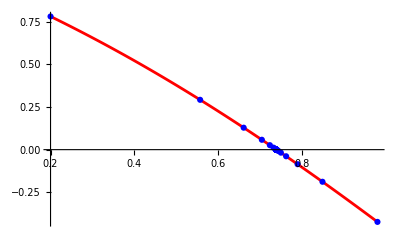

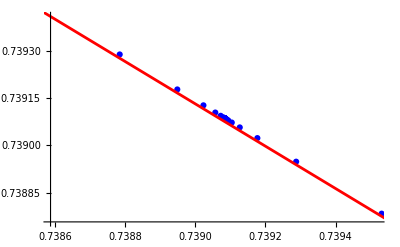

```mathematica
xMin=Min[pointsf[[All,1]]];
xMax=Max[pointsf[[All,1]]];
q := ListPlot[pointsf, PlotStyle->Blue];
rot := pointsf[[-1]][[1]];
p:= Plot[f[x], {x, xMin, xMax}, PlotStyle->Red];
a := ListPlot[pointsg, PlotStyle->Blue]
b:= Plot[g[x], {x, xMin, xMax}, PlotStyle->Red];
Print["root is: ", rot];
Show[p, q]
Show[a, b]
```

```mathematica
NSolve[f[x]==0,x,WorkingPrecision->20] (* {x->0.73908513321516064165531208767387341232`20.} *)
```

{{x→0.73908513321516064166},{x→-2.4868856989085602307+1.809361341295703319 ⅈ},{x→-9.1099874539365630068+2.950170861699436958 ⅈ},{x→-15.487957788766869181+3.456614935300047625 ⅈ},{x→-21.818976539497064446+3.79031255882446362 ⅈ},{x→-28.131612972193157125+4.039950881461228296 ⅈ},{x→-34.43496795188793658+4.239540266390788153 ⅈ},{x→-40.732927084395127975+4.405854262275104713 ⅈ},{x→-47.027449739772555271+4.548424206260374898 ⅈ},{x→-53.319638459569090925+4.673192083315506444 ⅈ},{x→-59.610164228277456943+4.784114503663495439 ⅈ},{x→-65.899460243746100363+4.88395960008406061 ⅈ},{x→-72.187819421019428906+4.97474014452765035 ⅈ},{x→-78.475447334138595195+5.05796567078960295 ⅈ},{x→-84.762492751386983418+5.13479743365585468 ⅈ},{x→-91.04906613536807704+5.20614795182825326 ⅈ}}